# ECUACIONES DIFERENCIALES

## ECUACIONES DIFERENCIALES LINEALES Y NO-LINEALES DE PRIMER ORDEN CON MATHEMATICA: CURVAS INTEGRALES O CURVAS SOLUCIÓN

Dr. Jorge Chávez Carlos

Una Ecuación Lineal de Primer Orden siempre puede escribirse como :

y'(x)+p(x)y(x)=q(x)

O para el caso No - Lineal de Primer Orden:

y'(x)=f(x,y)

Con mathematica es posible calcular la solución de ecuaciones diferenciales (Sin importar el orden de la ecuación) usando un comando muy sencillo de usar dado por:

DSolve[eqn,y,x]

Una vez resuelta la ecuación diferencial se procederá a graficar las curvas solución usando un comando muy sencillo de usar dado por:

ContourPlot[f,{x,x_min,x_max},{y,y_min,y_max}]

## Ejemplo: y'[x] + (2/x)y[x] = Cos[x]/x^2

Si uno solo quiere resolver la ecuación solo se teiene que escribir :

```mathematica
DSolve[y'[x] + (2/x)y[x] == Cos[x]/x^2,y[x],x]
```

{{y[x]→C[1]/x^2+Sin[x]/x^2}}

Por lo tanto la solución general es :

x^2 y-Sin[x]=C

Para graficar las curvas solución se escribe:

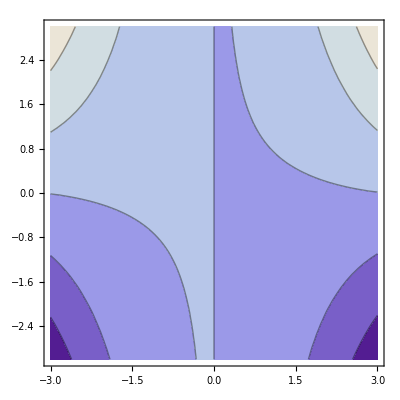

```mathematica
ContourPlot[x^2 y-Sin[x],{x,-3,3},{y,-3,3}]
```

Uno puede estilizar las curvas usando las multiples opciones de graficado como por ejemplo :

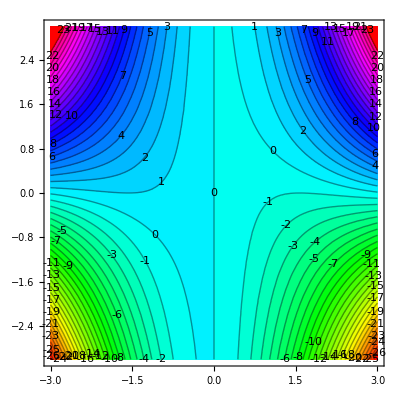

```mathematica
ContourPlot[x^2 y-Sin[x],{x,-3,3},{y,-3,3},ContourLabels->True,ColorFunction->Hue,Contours->50]
```

## Ejemplo 2: y'[x]= y Cos[x]/(1+2 y^2) Visto en clase (18-08-14)

La solución de dicha ecuación es: Log[Abs[y]]+y^2-Sin[x]=C

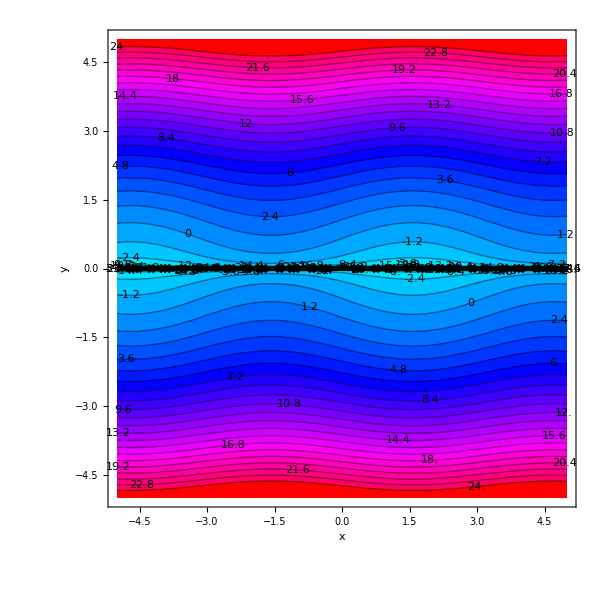

```mathematica
ContourPlot[Log[Abs[y]]+y^2-Sin[x],{x,-5,5},{y,-5,5},ContourLabels->True,ColorFunction->Hue,Contours->50,ImageSize-> 600,FrameLabel->{x,y}]
```